## Some basic plotting

Below are some quick code snippets to provide an idea of how to plot various quantities.

### Find directories with data

Work in the notebook directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Get a list of subdirectories with log.txt files, indicative of run data

```mathematica
directories = DirectoryName/@FileNames["log.txt","build",∞]
```

{build\dust_test\,build\lambda_test\,build\scalar_test\}

### Plot Reference FRW values

Output at https://github.com/jbcm627/cosmograph/blob/master/IO/io.cc#L193

```mathematica
frwfiles = FileNames["*.frwdat.*",directories,∞]
frwdata=Import/@frwfiles;
```

{build\dust_test\calculated.frwdat.gz,build\lambda_test\calculated.frwdat.gz,build\scalar_test\calculated.frwdat.gz}

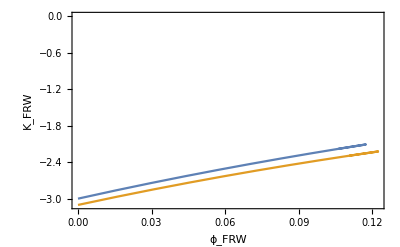

```mathematica
ListPlot[
frwdata⟦;;,;;,{1,2}⟧,
Joined->True,Axes->False,Frame->True,
FrameLabel->{"ϕ_FRW","K_FRW"}
]
```

### Plot metric statistics

Output at https://github.com/jbcm627/cosmograph/blob/master/IO/io.cc#L217

```mathematica
statfiles = FileNames["calculated.dat.gz",directories,∞]
statdata = Import/@statfiles;
```

{build\dust_test\calculated.dat.gz,build\lambda_test\calculated.dat.gz,build\scalar_test\calculated.dat.gz}

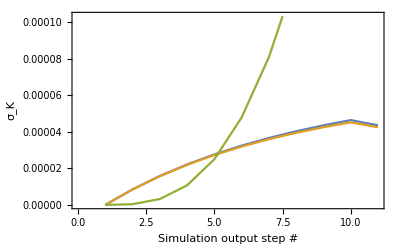

```mathematica
ListPlot[
statdata⟦;;,;;,4⟧,
Joined->True,Axes->False,Frame->True,
FrameLabel->{"Simulation output step #","σ_K"}
]
```

### Plot Constraint Violation

Output at https://github.com/jbcm627/cosmograph/blob/master/IO/io.cc#L154

```mathematica
Hviolfiles = FileNames["H_violations.dat.gz",directories,∞]
Hviol=Import/@Hviolfiles;
Mviolfiles = FileNames["M_violations.dat.gz",directories,∞]
Mviol = Import/@Mviolfiles;
```

{build\dust_test\H_violations.dat.gz,build\lambda_test\H_violations.dat.gz,build\scalar_test\H_violations.dat.gz}

{build\dust_test\M_violations.dat.gz,build\lambda_test\M_violations.dat.gz,build\scalar_test\M_violations.dat.gz}

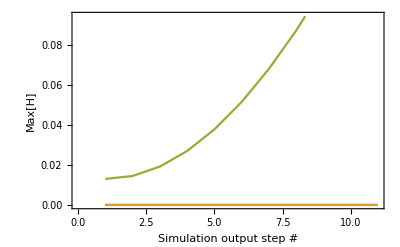

```mathematica
ListPlot[
Hviol⟦;;,;;,4⟧,
Joined->True,Axes->False,Frame->True,
FrameLabel->{"Simulation output step #","Max[H]"}
]
```

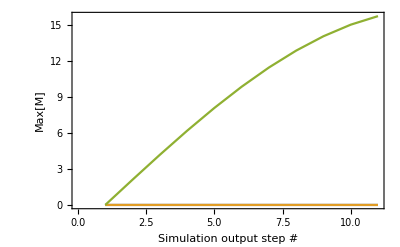

```mathematica
ListPlot[
Mviol⟦;;,;;,4⟧,
Joined->True,Axes->False,Frame->True,
FrameLabel->{"Simulation output step #","Max[M]"}
]
```

### Plot 1-d, 2-d, 3-d initial data from Δϕ field

#### 3 - D

```mathematica
Δϕfiles3D=FileNames["3D_DIFFphi.0.3d_grid.h5.gz",directories,∞]
Δϕ3D=Import[#,{"Datasets","DS1"}]&/@Δϕfiles3D;
```

{build\dust_test\3D_DIFFphi.0.3d_grid.h5.gz,build\lambda_test\3D_DIFFphi.0.3d_grid.h5.gz,build\scalar_test\3D_DIFFphi.0.3d_grid.h5.gz}

```mathematica
GraphicsGrid[{
ListDensityPlot3D/@Δϕ3D
}]
```

-Graphics-

#### 2 - D

```mathematica
Δϕfiles2D=FileNames["2D_DIFFphi.0.2d_grid.h5.gz",directories,∞]
Δϕ2D=Import[#,{"Datasets","Dataset1"}]&/@Δϕfiles2D;
```

{build\dust_test\2D_DIFFphi.0.2d_grid.h5.gz,build\lambda_test\2D_DIFFphi.0.2d_grid.h5.gz,build\scalar_test\2D_DIFFphi.0.2d_grid.h5.gz}

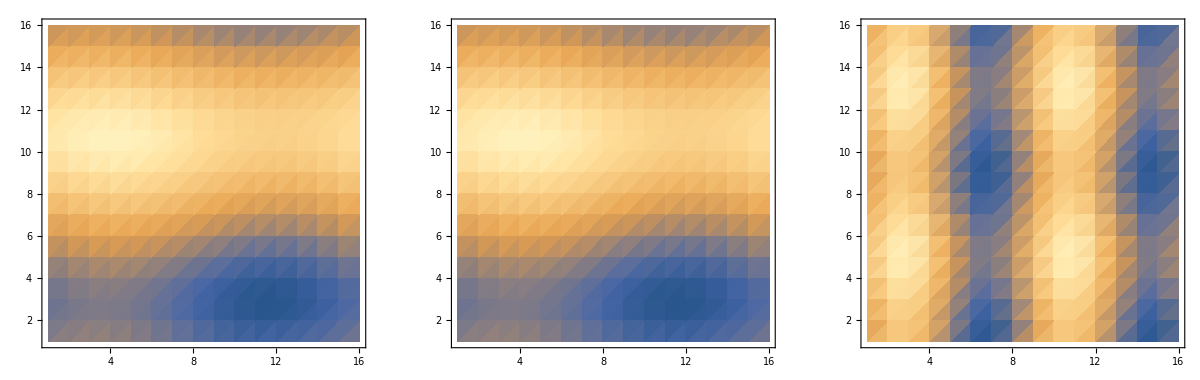

```mathematica
GraphicsGrid[{
ListDensityPlot/@Δϕ2D
}]
```

#### 1 - D

```mathematica
Δϕfiles1D=FileNames["1D_DIFFphi.strip.dat.gz",directories,∞]
Δϕ1D=Import[#]&/@Δϕfiles1D;
```

{build\dust_test\1D_DIFFphi.strip.dat.gz,build\lambda_test\1D_DIFFphi.strip.dat.gz,build\scalar_test\1D_DIFFphi.strip.dat.gz}

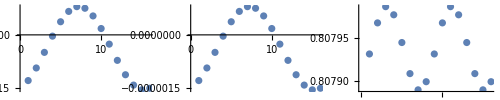

```mathematica
GraphicsGrid[{
ListPlot/@Δϕ1D⟦;;,1,;;⟧
},ImageSize->500]
```